# Quad Prog min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

## 16.6 Interior Point method Implementation Algorithm 16.4 p484/506 min 0.5 x.G.x+c.x A.x≥b

Initialize with feasible point (x_0,y_0,λ_0) i.e. y_0=A.x_0-b≥0_n and λ_0≥0_n

Iterate “to convergence” k=0,1,2,3,…

(x,y,λ)=(x_k,y_k,λ_k) and solve (16.58) with σ=0 to get (Δx^aff,Δy^aff,Δλ^aff).

Calculate μ=(y.λ)/m

Calculate (α̂)_aff=Max[0≤a≤1: (y,λ)+α(Δy^aff,Δλ^aff)≥0]

Calculate μ_aff=((y +  (α̂)_aff Δy^aff).(λ + (α̂)_aff Δλ^aff))/m

Set σ=(μ_aff/μ)^3

Solve 16.67 for (Δx,Δy,Δλ)

Choose τ_k∈(0,1) and set α̂=min(α_τ_k^pri,α_τ_k^dual) (see 16.66)

Update (x_k,y_k,λ_k)=(x_k,y_k,λ_k)+α̂(Δx,Δy,Δλ)

There is quite a lot of stuff to be defined and explained here! First
	(16.58) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-Λ.Y.e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b)
-Λ.Y.e+σ μ e)
is just the Newton step.  Step 2.2 just estimates how far from “complementarity” the original point is. Step 2.3 works out how far you can go in the affine “Newton” direction and maintain feasibility.  Step 2.4 checks how far from “complementarity” the new trial point is.  Step 2.5 computes a new value for σ from the two complementarity gaps. Step 2.6 uses that σ in the Newton Step with the affine Λ and Y
	(16.67) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b)
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)
Step 2.7 chooses maximum primal and dual steps sizes with the same safety factor τ
	(16.66) 	 α_τ^pri | = | Max[0≤α≤1:y+α Δy≥(1-τ)y]
α_τ^dual | = | Max[0≤α≤1:λ+α Δλ≥(1-τ)λ]
The Min ensures that both the updated slack variables y and updated Lagrange multipliers λ satisfy the feasibility conditions y+α̂ Δy≥0 and λ+α̂ Δλ≥0.  All of this manipulation is motivated by experience in the linear programming case and is designed to ensure that the “Newton” steps maintain feasibility.

Here are my code building blocks

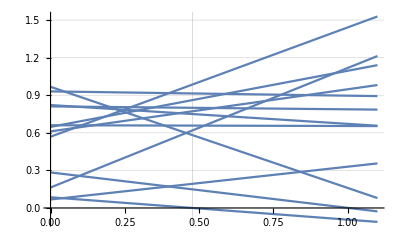

```mathematica
n=12;
ys=RandomReal[{0,1}, n];
Δys=RandomReal[{-1, 1}, n];
τ=1;
αTest=αStepComp[ys,Δys,τ];
Plot[ ys + α Δys,{α,0, 1.1},
GridLines->{{αTest}, Automatic}]
```

```mathematica
(* Generic Matrix *)
NewtonMatrix[G_,A_,λ_,y_]:= Module[{m=Length[G],n=Length[λ]},
ArrayFlatten[({{G, 0, -Aᵀ}, {A, -IdentityMatrix[n], 0}, {0, DiagonalMatrix[λ], DiagonalMatrix[y]}})]
]
(* Two different right hand sides for 11.58 and 11.67 *)
RHS58[G_,x_,A_,λ_,c_,y_,b_,σ_,μ_]:=Join[ -(G.x-Aᵀ.λ+c),-(A.x-y-b),-λ*y+σ μ]
RHS67[{G_,x_,A_,λ_,c_,y_,b_,σ_,μ_},{ΔλAff_,ΔyAff_}]:=Join[ -(G.x-Aᵀ.λ+c),-(A.x-y-b),-λ*y-ΔλAff*ΔyAff+σ μ]
(* maximum feasible step *)
αStepComp[y_,Δy_,τ_]:=Module[{αs=-τ y/Δy},
αs=Select[αs, #>0&];
Min[1,Min[αs]]
]
```

Build out the iteration manually.

```mathematica
{m,n}={6,3};
(* Test problem for objective *)
G=RandomReal[{-1,1},{m,m}];G=G+Gᵀ;
c=RandomReal[{-1,1},m];
(* test problem for constraints *)
A=RandomReal[{-1,1},{n,m}];
b=RandomReal[{-1,-0.01},n];
(* Simple feasible Initial Conditions *)
(* By construction the origin is feasible *)
x0=0*c;
λ0=ConstantArray[1,n];
y0=A.x0-b;
(* Initialize iteration variables *)
{x,λ,y}={x0,λ0,y0};
(* compute feasibility gap *)
μ=(y.λ)/m;
(* Construct Newton Matrix *)
NMat=NewtonMatrix[G,A,λ,y];
(* Compute Affine Step *)
σ=0.0;
RHSA = RHS58[G,x,A,λ,c,y,b,σ,μ];
ΔxΔyΔλA=LinearSolve[NMat,RHSA];
{ΔxA,ΔyA,ΔλA}={ΔxΔyΔλA⟦1;;m⟧,ΔxΔyΔλA⟦m+1;;m+n⟧,ΔxΔyΔλA⟦m+n+1;;m+2n⟧};
(* Compute max feasible Affine Step length *)
(* full step τ=1 *)
τ=1.0;
αHatA=αStepComp[Join[λ,y],Join[ΔλA,ΔyA],τ];
(* Update centering parameter σ *)
μA=(y+αHatA*ΔyA).(λ+αHatA*ΔλA)/m;
σ=(μA/μ)^3;
(* Solve 16.67 *)
RHS = RHS67[{G,x,A,λ,c,y,b,σ,μ},{ΔλA,ΔyA}];
ΔxΔyΔλ=LinearSolve[NMat,RHS];
{Δx,Δy,Δλ}={ΔxΔyΔλ⟦1;;m⟧,ΔxΔyΔλ⟦m+1;;m+n⟧,ΔxΔyΔλ⟦m+n+1;;m+2n⟧};
(* Compute max step lengths *)
(* safety factor 0<τ<1 *)
τ=0.9;
αPri=αStepComp[y,Δy,τ];
αDual=αStepComp[λ,Δλ,τ];
αHat=Min[αPri,αDual];
(* Update with step size αHat *)
{x,y,λ}={x,y,λ}+αHat{Δx,Δy,Δλ};
(* Check slacks are appropriately defined *)
Norm[y-(A.x-b)]
(* Check signs on slacks and multipliers *)
{y,λ}
```

1.57621×10^-16

{{0.971662,0.0888388,0.938246},{0.135348,0.1,0.232889}}

Build stepper function from script above.

```mathematica
InteriorPointStepper[{G_,c_},{A_,b_}][{x_,y_,λ_}]:= Module[
{m=Length[c],n=Length[b],μ, NMat,σ,RHSA,ΔxΔyΔλA,ΔxA,ΔyA,ΔλA,τ,
αHatA,μA,RHS,ΔxΔyΔλ,Δx,Δy,Δλ,αPri,αDual,αHat},
(* compute feasibility gap *)
μ=(y.λ)/m;
(* Construct Newton Matrix *)
NMat=NewtonMatrix[G,A,λ,y];
(* Compute Affine Step *)
σ=0.0;
RHSA = RHS58[G,x,A,λ,c,y,b,σ,μ];
ΔxΔyΔλA=LinearSolve[NMat,RHSA];
{ΔxA,ΔyA,ΔλA}={ΔxΔyΔλA⟦1;;m⟧,ΔxΔyΔλA⟦m+1;;m+n⟧,ΔxΔyΔλA⟦m+n+1;;m+2n⟧};
(* Compute max feasible Affine Step length *)
(* full step τ=1 *)
τ=1.0;
αHatA=αStepComp[Join[λ,y],Join[ΔλA,ΔyA],τ];
(* Update centering parameter σ *)
μA=(y+αHatA*ΔyA).(λ+αHatA*ΔλA)/m;
σ=(μA/μ)^3;
(* Solve 16.67 *)
RHS = RHS67[{G,x,A,λ,c,y,b,σ,μ},{ΔλA,ΔyA}];
ΔxΔyΔλ=LinearSolve[NMat,RHS];
{Δx,Δy,Δλ}={ΔxΔyΔλ⟦1;;m⟧,ΔxΔyΔλ⟦m+1;;m+n⟧,ΔxΔyΔλ⟦m+n+1;;m+2n⟧};
(* Compute max step lengths *)
(* safety factor 0<τ<1 *)
τ=0.9;
αPri=αStepComp[y,Δy,τ];
αDual=αStepComp[λ,Δλ,τ];
αHat=Min[αPri,αDual];
(* Update with step size αHat *)
{x,y,λ}+αHat{Δx,Δy,Δλ}
]
```

Build  test problem and compute some steps

```mathematica
{m,n}={15,8};
(* Test problem for objective *)
G=RandomReal[{-1,1},{m,m}];G=G+Gᵀ;
c=RandomReal[{-1,1},m];
(* test problem for constraints *)
A=RandomReal[{-1,1},{n,m}];
b=RandomReal[{-1,-0.01},n];
(* Simple feasible Initial Conditions. By construction the origin is feasible *)
{x,λ,y}={0*c,ConstantArray[1,n],-b};
(* Take some steps *)
MaxIter=353;
xyλData=Table[
{x,λ,y}=InteriorPointStepper[{G,c},{A,b}][{x,λ,y}],
{MaxIter}];
xData=xyλData⟦All,1⟧;
yData=xyλData⟦All,2⟧;
λData=xyλData⟦All,3⟧;
TabView[{
"x"->MatrixPlot[xData,PlotLegends->Automatic,FrameLabel->{"Iteration",None}],
"y"->MatrixPlot[yData,PlotLegends->Automatic,FrameLabel->{"Iteration",None}],
"λ"->MatrixPlot[λData,PlotLegends->Automatic,FrameLabel->{"Iteration",None}],
"y*λ"->MatrixPlot[yData*λData,PlotLegends->Automatic,FrameLabel->{"Iteration",None}]
}]
```

1234

Lets check the convergence etc.

```mathematica
ResData=Table[
{xx,yy,λλ}={xData⟦i⟧,yData⟦i⟧,λData⟦i⟧};
Norm[G.xx-Aᵀ.λλ+c],
{i,MaxIter}];
CompData=Table[
{xx,yy,λλ}={xData⟦i⟧,yData⟦i⟧,λData⟦i⟧};
MinMax[λλ*yy],
{i,MaxIter}]ᵀ;
TabView[{
"Residual"->ListLogPlot[ResData],
"y"->ListLogPlot[yDataᵀ,PlotLegends->Automatic],
"CompSlack"->ListLogPlot[CompData,PlotLegends->{"min","max"},
PlotRange->{10^-64,1}]
}
]
```

123

Lets start thinking about instrumenting mathematica and matlab

```mathematica
Clear[x,y]
s=1;
FindMinimum[{(x-2)^2+(y-3)^2, x^2+y^2<1},{{x,0.1},{y,0.1}},
Method->"InteriorPoint",
StepMonitor:>Print[s++," ",{x,y}]]
```

1 {0.1,0.1}

2 {0.171456,0.211456}

3 {0.949716,1.42102}

4 {0.783633,1.17465}

5 {0.65753,0.986174}

6 {0.585173,0.87775}

7 {0.558574,0.83786}

8 {0.554783,0.832175}

{6.7889,{x→0.5547,y→0.83205}}

```mathematica
s=1;
FindMinimum[{(x-2)^2+(y-3)^2, {x^2+y^2<1, x+y>0}},{{x,0.1},{y,0.1}},
Method->"InteriorPoint",
StepMonitor:>Print[s++," ",{x,y}]]
```

1 {0.1,0.1}

2 {0.175122,0.214912}

3 {1.09247,1.615}

4 {1.09286,1.61567}

5 {1.09084,1.61289}

6 {0.668694,1.03118}

7 {0.618782,0.93423}

8 {0.576338,0.865174}

9 {0.557735,0.836631}

10 {0.554709,0.832063}

11 {0.5547,0.83205}

{6.7889,{x→0.5547,y→0.83205}}

```mathematica
?NMinimize
```

```mathematica
Clear[x,y]
s=1;
NMinimize[{(x-2)^2+(y-3)^2,x^2+y^2<1},{x,y},
Method->"NelderMead",
StepMonitor:>Print[s++,{x,y}]
]
```

1{0.75721,0.152402}

2{0.75721,0.152402}

3{0.29367,1.10091}

4{0.29367,1.10091}

5{0.29367,1.10091}

6{0.29367,1.10091}

7{0.620525,0.940096}

8{0.620525,0.940096}

9{0.620525,0.940096}

10{0.620525,0.940096}

11{0.613602,0.833434}

12{0.613602,0.833434}

13{0.613602,0.833434}

14{0.577305,0.864737}

15{0.577305,0.864737}

16{0.577305,0.864737}

17{0.577305,0.864737}

18{0.569831,0.882447}

19{0.589848,0.862368}

20{0.578572,0.868572}

21{0.612969,0.831516}

22{0.607616,0.825397}

23{0.607616,0.825397}

24{0.607616,0.825397}

25{0.607616,0.825397}

26{0.59432,0.826907}

27{0.577116,0.844234}

28{0.577116,0.844234}

29{0.577116,0.844234}

30{0.577116,0.844234}

31{0.561866,0.853653}

32{0.571445,0.841034}

33{0.545735,0.853562}

34{0.545735,0.853562}

35{0.560985,0.844144}

36{0.554338,0.844898}

37{0.569587,0.83548}

38{0.561474,0.842166}

39{0.561474,0.842166}

40{0.561474,0.842166}

41{0.560704,0.842014}

42{0.55641,0.844273}

43{0.557935,0.841982}

44{0.550111,0.845356}

45{0.549248,0.842462}

46{0.549248,0.842462}

47{0.549248,0.842462}

48{0.549248,0.842462}

49{0.549248,0.842462}

50{0.551776,0.84076}

51{0.551034,0.838733}

52{0.555719,0.834315}

53{0.555719,0.834315}

54{0.555719,0.834315}

55{0.552891,0.836811}

56{0.554834,0.835661}

57{0.554834,0.835661}

58{0.554834,0.835661}

59{0.556269,0.834606}

60{0.556269,0.834606}

61{0.557145,0.833754}

62{0.555588,0.834586}

63{0.559221,0.831619}

64{0.557923,0.8318}

65{0.557923,0.8318}

66{0.557923,0.8318}

67{0.557923,0.8318}

68{0.557923,0.8318}

69{0.556593,0.832639}

70{0.556593,0.832639}

71{0.556086,0.832733}

72{0.557986,0.831197}

73{0.555051,0.832729}

74{0.555051,0.832729}

75{0.555051,0.832729}

76{0.555051,0.832729}

77{0.555051,0.832729}

78{0.555051,0.832729}

79{0.555051,0.832729}

80{0.555051,0.832729}

81{0.555112,0.832663}

82{0.554818,0.832831}

83{0.555226,0.832512}

84{0.554842,0.832689}

85{0.555468,0.832141}

86{0.555012,0.832221}

87{0.555012,0.832221}

88{0.555347,0.832108}

89{0.555347,0.832108}

90{0.555073,0.832238}

91{0.555789,0.831715}

92{0.555599,0.831714}

93{0.556316,0.831192}

94{0.556316,0.831192}

95{0.556,0.831387}

96{0.555879,0.831502}

97{0.555186,0.831951}

98{0.555186,0.831951}

99{0.554606,0.832344}

100{0.554695,0.832273}

101{0.554623,0.831749}

102{0.5547,0.83205}

103{0.5547,0.83205}

104{0.59429,0.891434}

105{0.565584,0.848376}

106{0.557496,0.836245}

107{0.555404,0.833106}

108{0.554877,0.832315}

109{0.554744,0.832116}

110{0.554711,0.832067}

111{0.554703,0.832054}

112{0.554702,0.832051}

113{0.554702,0.832049}

114{0.554702,0.832049}

115{0.554702,0.832049}

116{0.554702,0.832049}

117{0.554702,0.832049}

{6.7889,{x→0.554702,y→0.832049}}